```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2943 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
(* See James Clerk Maxwell , on governors  *)
```

```mathematica
Clear[ Ω0 ] 
Ω0 = { 0 , 0 , ω0 }
```

{0,0,ω0}

```mathematica
Clear[r1]
r1 = { - l Sin[θ[t]] , 0 , - l Cos[θ[t]] }
```

{-l Sin[θ[t]],0,-l Cos[θ[t]]}

```mathematica
D[r1, t] + Cross[ Ω0 , r1 ]  (* Minus sign second component or listed backwards ? *)
```

{-l Cos[θ[t]] θ'[t],-l ω0 Sin[θ[t]],l Sin[θ[t]] θ'[t]}

```mathematica
( D[r1, t] + Cross[ Ω0 , r1 ] ) . ( D[r1, t] + Cross[ Ω0 , r1 ] ) // Expand  // Simplify
```

l^2 (ω0^2 Sin[θ[t]]^2+θ'[t]^2)

```mathematica
Clear[r2]
r2 = { l Sin[θ[t]] , 0 , - l Cos[θ[t]] }
```

{l Sin[θ[t]],0,-l Cos[θ[t]]}

```mathematica
D[r2, t] + Cross[ Ω0 , r2 ]
```

{l Cos[θ[t]] θ'[t],l ω0 Sin[θ[t]],l Sin[θ[t]] θ'[t]}

```mathematica
( D[r2, t] + Cross[ Ω0 , r2 ]  ) . ( D[r2, t] + Cross[ Ω0 , r2 ]  )  // Expand // Simplify
```

l^2 (ω0^2 Sin[θ[t]]^2+θ'[t]^2)

```mathematica
Clear[r3]
r3 = { 0 , 0 , - 2 l Cos[θ[t]] }
```

{0,0,-2 l Cos[θ[t]]}

```mathematica
D[r3, t] + Cross[ Ω0 , r3 ]
```

{0,0,2 l Sin[θ[t]] θ'[t]}

```mathematica
( D[r3, t] + Cross[ Ω0 , r3 ]  ) . ( D[r3, t] + Cross[ Ω0 , r3 ]  ) // Expand // Simplify
```

4 l^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
Clear[𝓇]
𝓇 = { r1 , r2 , r3 }
```

{{-l Sin[θ[t]],0,-l Cos[θ[t]]},{l Sin[θ[t]],0,-l Cos[θ[t]]},{0,0,-2 l Cos[θ[t]]}}

```mathematica
Table[D[𝓇[[i]], t] + Cross[ Ω0 , 𝓇[[i]] ] , { i, 1, 3 } ] // MatrixForm
```

(-l Cos[θ[t]] θ'[t] | -l ω0 Sin[θ[t]] | l Sin[θ[t]] θ'[t]
l Cos[θ[t]] θ'[t] | l ω0 Sin[θ[t]] | l Sin[θ[t]] θ'[t]
0 | 0 | 2 l Sin[θ[t]] θ'[t])

```mathematica
Table[
( D[𝓇[[i]], t] + Cross[ Ω0 , 𝓇[[i]] ] ) . ( D[𝓇[[i]], t] + Cross[ Ω0 , 𝓇[[i]] ] ), 
{ i, 1, 3 } ] // Expand // Simplify  // MatrixForm
```

(l^2 (ω0^2 Sin[θ[t]]^2+θ'[t]^2)
l^2 (ω0^2 Sin[θ[t]]^2+θ'[t]^2)
4 l^2 Sin[θ[t]]^2 θ'[t]^2)

```mathematica
Clear[ℳ]
ℳ = { m , m, M }
```

{m,m,M}

```mathematica
Clear[T]
 T = 
Sum[ 
ℳ[[i]] ( ( D[𝓇[[i]], t] + Cross[ Ω0 , 𝓇[[i]]] ) . ( D[𝓇[[i]], t] + Cross[ Ω0 , 𝓇[[i]] ] ) ) , { i, 1, 3 } ]  // TrigExpand  // Simplify
```

2 l^2 (m ω0^2 Sin[θ[t]]^2+(m+M-M Cos[2 θ[t]]) θ'[t]^2)

```mathematica
𝓇[[1,3]]
𝓇[[2,3]]
𝓇[[3,3]]
```

-l Cos[θ[t]]

-l Cos[θ[t]]

-2 l Cos[θ[t]]

```mathematica
Clear[V]
V = 
Sum[ ℳ[[i]] g  𝓇[[i,3]] , { i, 1, 3 } ] // Simplify
```

-2 g l (m+M) Cos[θ[t]]

```mathematica
Clear[ℒ]
ℒ = T - V ;
ℒ // pdConv
```

2 g l (m+M) cos(θ(t))+2 l^2 (((∂θ(t))/(∂t))^2 (m-M cos(2 θ(t))+M)+m ω0^2 sin^2(θ(t)))

```mathematica
Clear[q]
q = θ[t]
```

θ[t]

```mathematica
D[ D[ ℒ , D[q, t] ], t ]  - D[ ℒ , q ] // Expand // Simplify  // TraditionalForm
```

2 l (g m sin(θ(t))+g M sin(θ(t))+2 l θ''(t) (m-M cos(2 θ(t))+M)-l m ω0^2 sin(2 θ(t))+2 l M (θ'(t))^2 sin(2 θ(t)))

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // pdConv
```

2 l (-sin(θ(t)) (g (m+M)-2 l m ω0^2 cos(θ(t)))-2 l (∂^2 θ(t))/(∂t^2) (m-M cos(2 θ(t))+M)-2 l M ((∂θ(t))/(∂t))^2 sin(2 θ(t)))==0

```mathematica
Clear[eq1]
eq1 = 
eqs  /. θ[t]-> θ0  /. θ'[t] -> 0  /. θ''[t] -> 0
```

-2 l (g (m+M)-2 l m ω0^2 Cos[θ0]) Sin[θ0]==0

```mathematica
Solve[ eq1 , θ0 ]  /. C[1]-> 0
```

{{θ0→0},{θ0→π},{θ0→ArcTan[(g (m+M))/(2 l m ω0^2),-(√(-g^2 m^2-2 g^2 m M-g^2 M^2+4 l^2 m^2 ω0^4))/(2 l m ω0^2)]},{θ0→ArcTan[(g (m+M))/(2 l m ω0^2),(√(-g^2 m^2-2 g^2 m M-g^2 M^2+4 l^2 m^2 ω0^4))/(2 l m ω0^2)]}}

```mathematica
eq1[[1,3]]== 0 
Solve[ eq1[[1,3]]== 0 , θ0 ]  /. C[1]-> 0
```

g (m+M)-2 l m ω0^2 Cos[θ0]==0

{{θ0→-ArcCos[(g (m+M))/(2 l m ω0^2)]},{θ0→ArcCos[(g (m+M))/(2 l m ω0^2)]}}

```mathematica
eqs
```

2 l (-(g (m+M)-2 l m ω0^2 Cos[θ[t]]) Sin[θ[t]]-2 l M Sin[2 θ[t]] θ'[t]^2-2 l (m+M-M Cos[2 θ[t]]) θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
M-> 50 , 
m-> 10 , 
g-> 9.8 , 
l-> 0.5 , 
ω0-> 2 
} ;
parameters // TableForm
```

M→50
m→10
g→9.8
l→0.5
ω0→2

```mathematica
eqs /. parameters  // Expand
```

-588. Sin[θ[t]]+40. Cos[θ[t]] Sin[θ[t]]-50. Sin[2 θ[t]] θ'[t]^2-60. θ''[t]+50. Cos[2 θ[t]] θ''[t]==0

```mathematica
Clear[ics]
ics = { 
θ[0]== π/12 ,
θ'[0] == 0 
} ;
ics // TableForm
```

θ[0]==π/12
θ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ { eqs }  /. parameters , ics ] , q , { t, 0, 200 } ] ]
```

{θ[t]→InterpolatingFunction[…][t]}

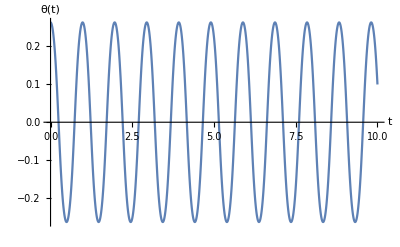

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t, 0, 10 }, AxesLabel-> { t , q }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q , D[q, t] } ]  ,
{ tmax , 1 ,75 , 0.5  } ]
```